```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

All Good!

All Good 1 !

All Good 2 !

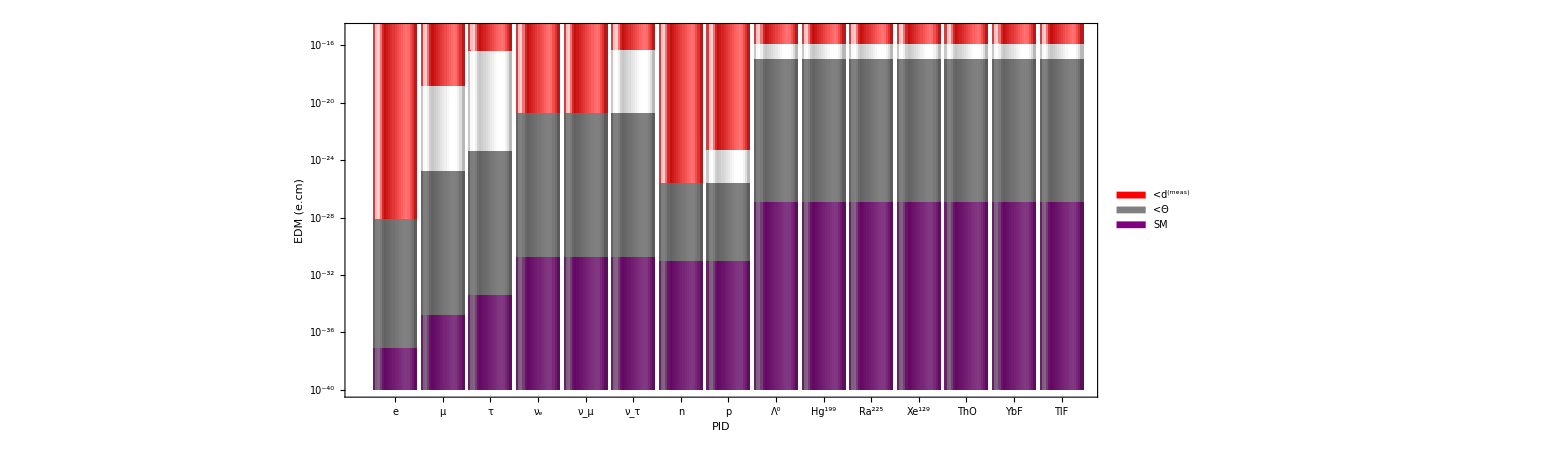

```mathematica
pttab1={
(*e*){8.6*N[10^(-38)],8.7*N[10^(-29)],0,N[10^(-10)]},
(*mu*){1.8*N[10^(-35)],1.8*N[10^(-25)],.9*1.64*N[10^(-19)],N[10^(-10)]},
(*τ*){4.5*N[10^(-34)],4.5*N[10^(-24)],4.5*N[10^(-17)],N[10^(-10)]},
(*nu_e*){1.73*5.7*N[10^(-26)]/(5*10^(5)),2*N[10^(-21)],0,N[10^(-10)]},
(*nu_mu*){3.59*5.7*N[10^(-24)]/(1.05*10^(8)),2*N[10^(-21)],0,N[10^(-10)]},
(*nu_τ*){6.03*5.7*N[10^(-23)]/(1.77*10^(9)),2*N[10^(-21)],5.2*N[10^(-17)],N[10^(-10)]},
(*n*){N[10^(-31)],2.9*N[10^(-26)],0,N[10^(-10)]},
(*p*){N[10^(-31)],2.9*N[10^(-26)],5.4*N[10^(-24)],N[10^(-10)]},
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]}
};
pttab2={
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]},
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]},
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]},
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]},
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]},
(*Λ*){7.4*1.64*N[10^(-28)],7.4*1.64*N[10^(-18)],7.4*1.64*N[10^(-17)],N[10^(-10)]}
};
pttab=Join[pttab1,pttab2];
particles1={"e","μ","τ","ν_e","ν_μ","ν_τ","n","p","Λ^0"};
particles2={"Hg^199","Ra^225","Xe^129","ThO","YbF","TlF"};
particles=Join[particles1,particles2];
(**Formatting**)
thk=.004;
If[Dimensions[pttab][[1]]==Dimensions[particles][[1]],Print["All Good!"],Print["Re-check data and names!"]];
If[Dimensions[pttab1][[1]]==Dimensions[particles1][[1]],Print["All Good 1 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab2][[1]]==Dimensions[particles2][[1]],Print["All Good 2 !"],Print["Re-check data and names!"]];
numpart=Dimensions[particles][[1]];
numpart1=Dimensions[particles1][[1]];
numpart2=Dimensions[particles2][[1]];
ptsty=-39;pteny=-9;ptinty=3;
gridln={Table[k,{k,1,numpart,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln1={Table[k,{k,1,numpart1,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln2={Table[k,{k,1,numpart2,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
tks={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles[[k]],{0.015,0}},{k,1,numpart}],None}};
tks1={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles1[[k]],{0.015,0}},{k,1,numpart1}],None}};
tks2={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles2[[k]],{0.015,0}},{k,1,numpart2}],None}};
cht=BarChart[pttab,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->{"SM","<Θ","","<d^(meas)"},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks,ChartStyle->{Purple,Gray,White,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.3,ImageSize->1600]
```

```mathematica
cht1=BarChart[pttab1,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->{"SM","<Θ","","<d^(meas)"},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks1,ChartStyle->{Purple,Gray,White,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.3*(numpart/numpart1),ImageSize->1600]
cht2=BarChart[pttab2,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->{"SM","<Θ","","<d^(meas)"},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks2,ChartStyle->{Purple,Gray,White,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.3*(numpart/numpart2),ImageSize->1600]
```